## Задача 1

Уравнение Шредингера для осциллятора имеет вид
-ψ''[x]/2+x^2/2 ψ[x]=E ψ[x]
Найти 3 минимальных уровня энергии E_n  (n=0,1,2)
и нарисовать соответствующие им волновые функции
ψ_n[x].

## Решение

Уровни энергии положительны, E>0.

Все собственные функции - четные или нечетные!

```mathematica
x1=5;
```

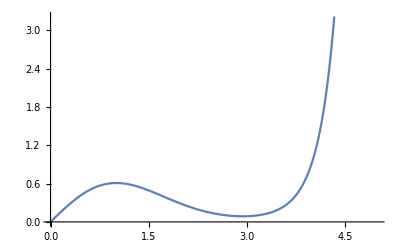

```mathematica
EE=1.49;
solution=NDSolve[{-ψ''[x]+x^2 ψ[x]== 2 EE ψ[x],ψ[0]==0,ψ'[0]==1},
ψ,{x,0,x1}][[1]];
Plot[ψ[x]/.solution,{x,0,x1}]
```

```mathematica
x1=5;
```

```mathematica
Manipulate[
solution=NDSolve[{-ψ''[x]+x^2 ψ[x]== 2 EE ψ[x],ψ[0]==1,ψ'[0]==0},
ψ,{x,0,x1}][[1]];
Plot[ψ[x]/.solution,{x,0,x1}],
{EE,0,5}
]
```

NDSolve::ndnl: Endpoint x1 in {x,0.,x1} is not a real number.

Plot::plln: Limiting value x1 in {x,0,x1} is not a machine-sized real number.

NDSolve::ndnl: Endpoint x1 in {x,0.,x1} is not a real number.

Plot::plln: Limiting value x1 in {x,0,x1} is not a machine-sized real number.

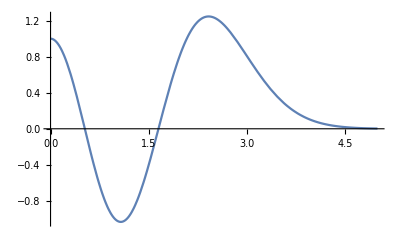

```mathematica
EE=4.5;
solution=NDSolve[{-ψ''[x]+x^2 ψ[x]== 2 EE ψ[x],ψ[0]==1,ψ'[0]==0},
ψ,{x,0,x1}][[1]];
Plot[ψ[x]/.solution,{x,0,x1}]
```

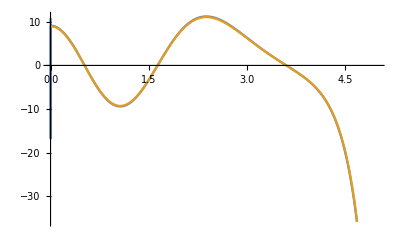

```mathematica
Plot[{-ψ''[x]+x^2 ψ[x]/.solution,
2 EE ψ[x]/.solution},{x,0,x1}]
```